```mathematica
(*Bayes theorem probability of the hypothesis:
P(lambda|{x1,...,xN}) = P({x1,...xN}|lambda))*P(lambda)/P({x}*)
(*Z normalizes the distribution over the range*)
Z[λ_]:=Integrate[(1/λ)*Exp[-x/λ],{x,1,20}]
```

ⅇ^(20/λ-x/λ)/((-1+ⅇ^(19/λ)) λ)

{2,5,10}

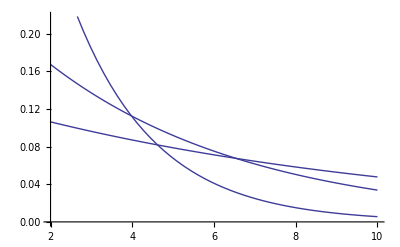

{3,5,12}

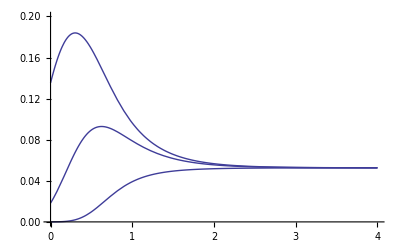

```mathematica
(*The probability of one data point given lambda is then:*)
P[x_,λ_]=((1/λ)*Exp[-x/λ])/(Integrate[(1/λ)*Exp[-x/λ],{x,1,20}])
λn={2,5,10}
Plot[Table[P[x,λn[[i]]],{i,1,3} ],{x,2,10}]
lisx={3,5,12}
Plot[Table[P[lisx[[i]],10^λ],{i,1,3} ],{λ,0,4}, PlotRange->{0,0.2}]
(*Plot[P[x,2],{x,0,10}]*)
(*P(x,lambda):= Probability of x given lambda={2,5,10}*)
```

{1.5,2,3,4,5,12}

{ⅇ^(18.5/λ)/((-1+ⅇ^(19/λ)) λ),ⅇ^(18/λ)/((-1+ⅇ^(19/λ)) λ),ⅇ^(17/λ)/((-1+ⅇ^(19/λ)) λ),ⅇ^(16/λ)/((-1+ⅇ^(19/λ)) λ),ⅇ^(15/λ)/((-1+ⅇ^(19/λ)) λ),ⅇ^(8/λ)/((-1+ⅇ^(19/λ)) λ)}

ⅇ^(92.5/λ)/((-1+ⅇ^(19/λ))^6 λ^6)

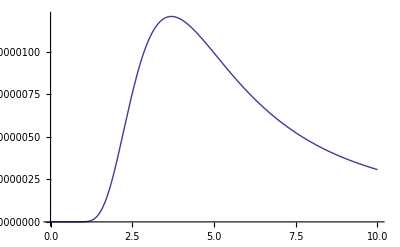

```mathematica
xn = {1.5, 2,3,4,5,12}
(*Now flip things on their head and say what is the probability of lambda given the data*)
(*P(lambda|{x1,...xN}*)
(*B[λ_,x_]= (1/(Integrate[(1/λ)*Exp[-x/λ],{x,1,20}]))^6*Exp[-(Sum[x,{x,{1.5, 2,3,4,5,12}}])/λ] *)
B[λ_]= Table[(1/(Integrate[(1/λ)*Exp[-x/λ],{x,1,20}]))*1/λ*Exp[-(xn[[i]])/λ] ,{i,1,6}]
f[λ_]=Times@@B[λ]
Plot[f[x],{x,0,10},PlotRange->Automatic]
```

```mathematica
(*As Gravy we can look at the Probability density as a function of x and lambda scaled logarithmically*)

Plot3D[P[x,Exp[λ]/100],{x,1,3},{λ,1,10}]
```

-Graphics3D-